```mathematica
x[r_]:=Integrate[1/f[r],r];
(*First derivative*)Print[D[Q[r],r]/D[x[r],r]];
(*Second derivative*)Print[Expand[D[D[Q[r],r]/D[x[r],r],r]/D[x[r],r]]];
(*Third derivative*)Print[Expand[D[D[D[Q[r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r]]];
(*Fourth derivative*)Print[Expand[D[D[D[D[Q[r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r]]];
(*Fifth derivative*)Print[Expand[D[D[D[D[D[Q[r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r]]];
(*Sixth derivative*)Print[Expand[D[D[D[D[D[D[Q[r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r],r]/D[x[r],r]]/D[x[r],r]]];
```

f[r] Q'[r]

f[r] f'[r] Q'[r]+f[r]^2 Q''[r]

f[r] f'[r]^2 Q'[r]+f[r]^2 Q'[r] f''[r]+3 f[r]^2 f'[r] Q''[r]+f[r]^3 Q^(3)[r]

f[r] f'[r]^3 Q'[r]
+4 f[r]^2 f'[r] Q'[r] f''[r]
+7 f[r]^2 f'[r]^2 Q''[r]
+4 f[r]^3 f''[r] Q''[r]
+f[r]^3 Q'[r] f^(3)[r]
+6 f[r]^3 f'[r] Q^(3)[r]
+f[r]^4 Q^(4)[r]

f[r] f'[r]^4 Q'[r]+11 f[r]^2 f'[r]^2 Q'[r] f''[r]+4 f[r]^3 Q'[r] f''[r]^2+15 f[r]^2 f'[r]^3 Q''[r]+30 f[r]^3 f'[r] f''[r] Q''[r]+7 f[r]^3 f'[r] Q'[r] f^(3)[r]+5 f[r]^4 Q''[r] f^(3)[r]+25 f[r]^3 f'[r]^2 Q^(3)[r]+10 f[r]^4 f''[r] Q^(3)[r]+f[r]^4 Q'[r] f^(4)[r]+10 f[r]^4 f'[r] Q^(4)[r]+f[r]^5 Q^(5)[r]

f[r]^2 f'[r]^4 Q'[r]+11 f[r]^3 f'[r]^2 Q'[r] f''[r]+4 f[r]^4 Q'[r] f''[r]^2+15 f[r]^3 f'[r]^3 Q''[r]+30 f[r]^4 f'[r] f''[r] Q''[r]+7 f[r]^4 f'[r] Q'[r] f^(3)[r]+5 f[r]^5 Q''[r] f^(3)[r]+25 f[r]^4 f'[r]^2 Q^(3)[r]+10 f[r]^5 f''[r] Q^(3)[r]+f[r]^5 Q'[r] f^(4)[r]+10 f[r]^5 f'[r] Q^(4)[r]+f[r]^6 Q^(5)[r]

```mathematica
initialSeedPoly[exp_,x_]:=Expand[exp/.{x->(x-Coefficient[exp,x^(Exponent[exp,x]-1)]/Exponent[exp,x])}];
stageTwoSeedPoly[exp_,x_]:=Expand[x^Exponent[exp,x]+Sum[-Abs[Coefficient[exp,x^i]]x^i,{i,1,Exponent[exp,x]-2}]-Abs[exp-Sum[Coefficient[exp,x^i]x^i,{i,1,Exponent[exp,x]}]]];
initialSeed[exp_,x_]:=
Block[
{n,exp1,i,c1},
i=0;
n =Exponent[exp,x];
c1=Coefficient[exp,x^(n-1)];
exp1=stageTwoSeedPoly[initialSeedPoly[exp,x],x];
While[
Not[And[(exp1/.x->i)≤0,(exp1/.x->i+1)≥0]],
i=i+1;
];
Return[Table[-c1/n+Round[i+1]Exp[I*(2Pi/n*(k-1)+Pi/2/n)],{k,1,n}]];
];
PACARootFinder[exp_,x_]:=If[
Exponent[exp,x]==1,
-(exp-x Coefficient[exp,x])/Coefficient[exp,x],
Block[
{n1,z,z1,i,flag},
n1=Exponent[exp,x];
z =N[initialSeed[exp,x]];
While[True,
z1 = Table[z[[i]]+(exp/.x->z[[i]])/((exp/.x->z[[i]])*Sum[If[k≠i,1/(z[[i]]-z[[k]]),0],{k,1,n1}]-(D[exp,x]/.x->z[[i]])),{i,1,n1}];
flag=True;
For[i=1,i≤n1,i++,flag=And[flag,Abs[z[[i]]-z1[[i]]]<0.01]];
If[flag,Break[]];
For[i=1,i≤n1,i++,z[[i]]=z1[[i]]];
];
Return[Round[z1,0.000001]];
]];
NewPACARootFinder[exp_,x_]:=
Block[
{n,cp,exp1,exp2,exp3,c0},
n=Exponent[exp,x];
cp=Coefficient[exp,x^n];
exp1=N[Expand[exp/cp]];
c0=exp1/.x->0;
(*Refining the coefficients*)
exp2=If[Abs[c0]<0.01,Sign[Re[c0]]0.01+I Sign[Im[c0]]0.01,Round[c0,0.01]]+Sum[ If[Abs[Coefficient[exp1,x^i]]<0.01,Sign[Re[Coefficient[exp1,x^i]]]0.01+I Sign[Im[Coefficient[exp1,x^i]]]0.01,Round[Coefficient[exp1,x^i] ,0.01]]*x^i,{i,1,n}];
cp=Coefficient[exp2,x^n];
exp3=N[Expand[exp2/cp]];
Return[PACARootFinder[exp3,x]]
];
```

```mathematica
VPotential[f_,r_,l_]:=f*(l*(l+1)/r^2+D[f,r]/r);
QFunction[f_,r_,l_,ω_]:=ω^2-VPotential[f,r,l];
ΛTildeFunction[f_,r_,n_,l_,ω_]:=
Block[
{α,r0,t0,t2,t3,t4,n1},
α=n+1/2;
t0=NSolve[D[QFunction[f,r,l,ω],r]==0,r];
n1=Length[t0];
r0=Max[Table[If[Im[t0[[i]][[1]][[2]]]==0,t0[[i]][[1]][[2]],0],{i,1,n1}]];
t2=(f D[f,r] D[QFunction[f,r,l,ω],r]+f^2D[QFunction[f,r,l,ω],{r,2}])/.{r->r0};
t3=(f D[f,r]^2 D[QFunction[f,r,l,ω],r]+f^2 D[QFunction[f,r,l,ω],r] D[f,r]+3 f^2 D[f,r] D[QFunction[f,r,l,ω],{r,2}]+f^3 D[QFunction[f,r,l,ω],{r,3}])/.{r->r0};
t4=(f D[f,r]^3 D[QFunction[f,r,l,ω],r]+4 f^2 D[f,r] D[QFunction[f,r,l,ω],r] D[f,{r,2}]+7 f^2 D[f,r]^2 D[QFunction[f,r,l,ω],{r,2}]+4 f^3 D[f,{r,2}] D[QFunction[f,r,l,ω],{r,2}]+f^3 D[QFunction[f,r,l,ω],r] D[f,{r,3}]+6 f^3 D[f,r] D[QFunction[f,r,l,ω],{r,3}]+f^4 D[QFunction[f,r,l,ω],{r,4}])/.{r->r0};
Return[-I/Sqrt[2t2]*(1/8*(t4/t2)(1/4+α^2)-1/288(t3/t2)^2(7+60α^2))]
];
ΩTildeFunction[f_,r_,n_,l_,ω_]:=
Block[
{α,r0,t0,t2,t3,t4,t6,n1},
α=n+1/2;
t0=NSolve[D[QFunction[f,r,l,ω],r]==0,r];
n1=Length[t0];
r0=Max[Table[If[Im[t0[[i]][[1]][[2]]]==0,t0[[i]][[1]][[2]],0],{i,1,n1}]];
t2=(f D[f,r] D[QFunction[f,r,l,ω],r]+f^2D[QFunction[f,r,l,ω],{r,2}])/.{r->r0};
t3=(f D[f,r]^2 D[QFunction[f,r,l,ω],r]+f^2 D[QFunction[f,r,l,ω],r] D[f,r]+3 f^2 D[f,r] D[QFunction[f,r,l,ω],{r,2}]+f^3 D[QFunction[f,r,l,ω],{r,3}])/.{r->r0};
t4=(f D[f,r]^3 D[QFunction[f,r,l,ω],r]+4 f^2 D[f,r] D[QFunction[f,r,l,ω],r] D[f,{r,2}]+7 f^2 D[f,r]^2 D[QFunction[f,r,l,ω],{r,2}]+4 f^3 D[f,{r,2}] D[QFunction[f,r,l,ω],{r,2}]+f^3 D[QFunction[f,r,l,ω],r] D[f,{r,3}]+6 f^3 D[f,r] D[QFunction[f,r,l,ω],{r,3}]+f^4 D[QFunction[f,r,l,ω],{r,4}])/.{r->r0};
t6=(f^2 D[f,r]^4 D[QFunction[f,r,l,ω],r]+11 f^3 D[f,r]^2D[QFunction[f,r,l,ω],r] f''[r]+4 f^4D[QFunction[f,r,l,ω],r] D[f,{r,2}]^2+15 f^3D[f,r]^3 D[QFunction[f,r,l,ω],{r,2}]+30 f^4 D[f,r] D[f,{r,2}] D[QFunction[f,r,l,ω],{r,2}]+7 f^4 D[f,r] D[QFunction[f,r,l,ω],r] D[f,{r,3}]+5 f^5D[QFunction[f,r,l,ω],{r,2}]D[f,{r,3}]+25 f^4 D[f,r]^2 D[QFunction[f,r,l,ω],{r,3}]+10 f^5D[f,{r,2}]D[QFunction[f,r,l,ω],{r,3}]+f^5 D[QFunction[f,r,l,ω],r] D[f,{r,4}]+10 f^5 D[f,r] D[QFunction[f,r,l,ω],{r,4}]+f^6 D[QFunction[f,r,l,ω],{r,5}])/.{r->r0};
Return[1/2/t2*(5/6912*(t3/t2)^4(77+188α^2)-1/384(t3^2t4/t2^3)(51+100α^2)+1/2304(t4/t2)^2(67+68α^2)-1/288(t6/t2)(5+4α^2))]
];
WKBEquations[f_,r_,n_,l_,ω_]:=
Block[
{n1,t0,r0,V0,V2},
t0=NSolve[D[VPotential[f,r,l],r]==0,r];
n1=Length[t0];
r0=Max[Table[If[Im[t0[[i]][[1]][[2]]]==0,t0[[i]][[1]][[2]],0],{i,1,n1}]];
V0=VPotential[f,r,l]/.{r->r0};
V2=D[VPotential[f,r,l],{r,2}]/.{r->r0};
Return[V0+Sqrt[-V2]/ΛTildeFunction[f,r,n,l,ω]-ω^2-I (n+1/2)Sqrt[-2V2](1+ΩTildeFunction[f,r,n,l,ω])]
];
PACAWKBGetModes[f_,r_,n_,l_,ω_]:=NewPACARootFinder[WKBEquations[f,r,n,l,ω],ω];
```

```mathematica
PACAWKBGetModes[1-2/r+3/r^3,r,1,0,ω]
```

{2.10476+2.1 ⅈ,-2.10476-2.1 ⅈ}

```mathematica
PACAWKBGetModes[1-μ/r+q/r^β/.{μ->2,β->3/2,q->0.1},r,1,3,ω]
```

{1.3251-1.12067 ⅈ,-1.3251+1.12067 ⅈ}

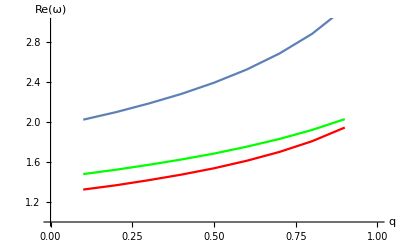

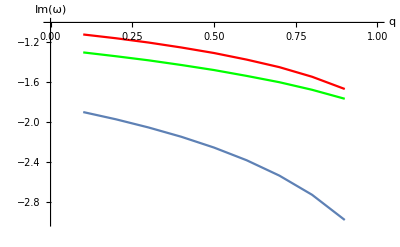

```mathematica
Block[
{μ,β,tab0,tab1,tab2},
μ=2;
β=3/2;
tab0=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,0,3,ω][[1]],{q,0.1,0.9,0.1}];
tab1=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,1,3,ω][[1]],{q,0.1,0.9,0.1}];
tab2=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,2,3,ω][[1]],{q,0.1,0.9,0.1}];
Print[Show[
ListLinePlot[Table[{0.1*i,Re[tab0[[i]]]},{i,1,9}]],
ListLinePlot[Table[{0.1*i,Re[tab1[[i]]]},{i,1,9}],PlotStyle->Red],
ListLinePlot[Table[{0.1*i,Re[tab2[[i]]]},{i,1,9}],PlotStyle->Green],
PlotRange->{{0,1},{1,3}},AxesOrigin->{0,1},AxesLabel->{q,Re[ω]}
]];
Print[Show[
ListLinePlot[Table[{0.1*i,Im[tab0[[i]]]},{i,1,9}]],
ListLinePlot[Table[{0.1*i,Im[tab1[[i]]]},{i,1,9}],PlotStyle->Red],
ListLinePlot[Table[{0.1*i,Im[tab2[[i]]]},{i,1,9}],PlotStyle->Green],
PlotRange->{{0,1},{-3,-1}},AxesOrigin->{0,-1},AxesLabel->{q,Im[ω]}
]];
]
```

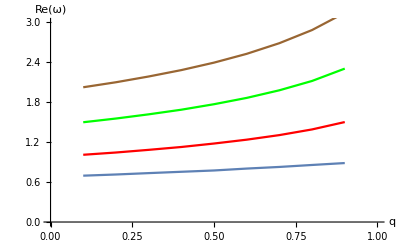

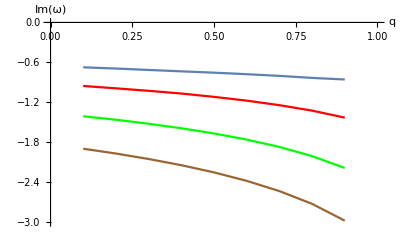

```mathematica
Block[
{μ,β,tab0,tab1,tab2,tab3},
μ=2;
β=3/2;
tab0=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,0,0,ω][[1]],{q,0.1,0.9,0.1}];
tab1=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,0,1,ω][[1]],{q,0.1,0.9,0.1}];
tab2=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,0,2,ω][[1]],{q,0.1,0.9,0.1}];
tab3=Table[PACAWKBGetModes[1-μ/r+q/r^β,r,0,3,ω][[1]],{q,0.1,0.9,0.1}];
Print[Show[
ListLinePlot[Table[{0.1*i,Re[tab0[[i]]]},{i,1,9}]],
ListLinePlot[Table[{0.1*i,Re[tab1[[i]]]},{i,1,9}],PlotStyle->Red],
ListLinePlot[Table[{0.1*i,Re[tab2[[i]]]},{i,1,9}],PlotStyle->Green],
ListLinePlot[Table[{0.1*i,Re[tab3[[i]]]},{i,1,9}],PlotStyle->Brown],
PlotRange->{{0,1},{0,3}},AxesOrigin->{0,0},AxesLabel->{q,Re[ω]}
]];
Print[Show[
ListLinePlot[Table[{0.1*i,Im[tab0[[i]]]},{i,1,9}]],
ListLinePlot[Table[{0.1*i,Im[tab1[[i]]]},{i,1,9}],PlotStyle->Red],
ListLinePlot[Table[{0.1*i,Im[tab2[[i]]]},{i,1,9}],PlotStyle->Green],
ListLinePlot[Table[{0.1*i,Im[tab3[[i]]]},{i,1,9}],PlotStyle->Brown],
PlotRange->{{0,1},{-3,0}},AxesOrigin->{0,0},AxesLabel->{q,Im[ω]}
]];
]
```

```mathematica
(1-(rp+2rp^3/R^2+Q^2/rp)/r+Q^2/r^2+r^2/R^2)/.{rp->50,R->2,Q->10}
```

1+100/r^2-62552/r+r^2/4

```mathematica
PACAWKBGetModes[(1-(rp+2rp^3/R^2+Q^2/rp)/r+Q^2/r^2+r^2/R^2)/.{rp->20,R->1,Q->10},r,1,0,ω]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 1+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 2+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Coefficient::ivar: 1 is not a valid variable.

Coefficient::ivar: 1. is not a valid variable.

General::stop: Further output of Coefficient::ivar will be suppressed during this calculation.

{}